```mathematica
11/20(1-10^-0.120)
11/220 (1-10^-0.1616)
```

0.132782

0.0155357

### Inhomogeneity Investigation

#### Dependence of N_C on v_E

The thought is that if the captured charge still acts to fill up the well and fill up the potential it is still a 1 parameter family of solutions. The only difference when we include the motion of the Earth, is that the N_C needed to affect this will depend on v_E  so let’s figure out what that will be. We worked out before that. 

Let’s for now imagine that we can trust the analysis we did before (even though we will likely need to modify it to account for the correct version from the paper we found)

(80 ⅇ^(-27/8-(3 v^2)/800) Sinh[9/80 √(-121+v^2)])/(9 √(-121+v^2))

0.265273

ⅇ^(-(3 v^2)/800)

4.93176

{ⅇ^(-(3 v^2)/800),(80 ⅇ^(-27/8-(3 v^2)/800) Sinh[9/80 √(-121+v^2)])/(9 √(-121+v^2)),(80 Sinh[9/80 √(-121+v^2)])/(9 ⅇ^(27/8) √(-121+v^2))}

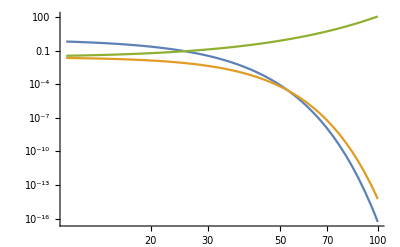

```mathematica
vEtemp = 30 (*kms^-1*);
v0disktemp = 20 (*kms^-1*);
fani = E^(-(3 vEtemp^2)/(2 v0disktemp^2))Sinh[x]/x/.x->(3 vEtemp)/(2 v0disktemp^2)√(#^2-vesc^2)&;
E^(-(3 v^2)/(2 v0disktemp^2))fani[v]/.vesc->11
NIntegrate[ %,{v,11,∞}]
E^(-(3 v^2)/(2 v0disktemp^2))/.vesc->11
NIntegrate[ %,{v,11,∞}]
{E^(-(3 v^2)/(2 v0disktemp^2)),E^(-(3 v^2)/(2 v0disktemp^2))fani[v],fani[v]}/.vesc->11
LogLogPlot[Evaluate@%,{v,11,100}]
```

```mathematica
Limit[fani[v],v->vesc]
```

1/ⅇ^(27/8)

(80 Sinh[(9 √(-vesc^2))/80])/(9 ⅇ^(27/8) √(-vesc^2))+(80 v^2 (-(9 Cosh[(9 √(-vesc^2))/80])/(160 vesc^2)+Sinh[(9 √(-vesc^2))/80]/(2 vesc^2 √(-vesc^2))))/(9 ⅇ^(27/8))

(80 Sinh[(9 v)/80])/(9 ⅇ^(27/8) v)

Piecewise[{{(80 Sinh[(9 v)/80])/(9 ⅇ^(27/8) v), v>10+vesc}, {(80 Sinh[(9 √(-vesc^2))/80])/(9 ⅇ^(27/8) √(-vesc^2))+(80 v^2 (-(9 Cosh[(9 √(-vesc^2))/80])/(160 vesc^2)+Sinh[(9 √(-vesc^2))/80]/(2 vesc^2 √(-vesc^2))))/(9 ⅇ^(27/8)), v<10+vesc}, {0, True}}]

{(80 Sinh[9/80 √(-121+v^2)])/(9 ⅇ^(27/8) √(-121+v^2)),Piecewise[{{(80 Sinh[(9 v)/80])/(9 ⅇ^(27/8) v), v>21}, {(80 v^2 (-(9 Cos[99/80])/19360+Sin[99/80]/2662))/(9 ⅇ^(27/8))+(80 Sin[99/80])/(99 ⅇ^(27/8)), v<21}, {0, True}}]}

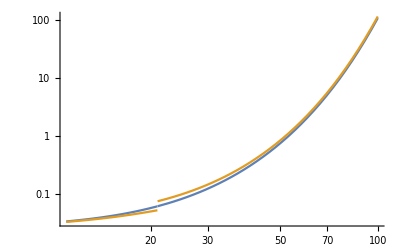

(19360 Sin[99/80]+v^2 (-99 Cos[99/80]+80 Sin[99/80]))/(23958 ⅇ^(27/8))

1/(35937 ⅇ^(4023/800))200 (63 (27753 Cos[99/80]-28880 Sin[99/80])+800 ⅇ^(1323/800) √(6 π) (Erf[(11 √(3/2))/20]-Erf[(21 √(3/2))/20]) (165 Cos[99/80]-214 Sin[99/80])+ⅇ^(6/5) (-567369 Cos[99/80]+671440 Sin[99/80]))

(80 Sinh[(9 v)/80])/(9 ⅇ^(27/8) v)

(2000 (-8+8 ⅇ^(189/40)+3 ⅇ^(243/50) √(6 π) (Erfc[(3 √(3/2))/10]+Erfc[(9 √(3/2))/5])))/(27 ⅇ^(5913/800))

```mathematica
fani[v](*/.v->vesc+ϵ*);
Series[%,{v,0,2}]//Normal
(*Series[%%,{v,∞,1}]//Normal*)
(80 Sinh[(9 v)/80])/(9 ⅇ^(27/8) v)
(*(80 Sinh[(9 vesc)/80+(9 (v-vesc))/80])/(9 ⅇ^(27/8) (v-vesc))*)
(*Piecewise[{{(80 Sinh[(9 vesc)/80-(9 vesc^2)/(160 (v-vesc))+(9 v)/80])/(9 ⅇ^(27/8) v),v>vesc+10},{1/ⅇ^(27/8)+(27 vesc v)/(6400 ⅇ^(27/8))+(27 (32000+81 vesc^2) v^2)/(409600000 ⅇ^(27/8)),v<vesc+10}}]*)
Piecewise[{{%/.ϵ->v-vesc,v>vesc+10},{%%/.ϵ->v-vesc,v<vesc+10}}]
(*(%/.ϵ->v-vesc)Boole[v>vesc+10]+(%%/.ϵ->v-vesc)Boole[v<vesc+10]*)
{fani[v],%}/.vesc->11
LogLogPlot[Evaluate@%,{v,11,100}]
Assuming[v<21,%%[[2]]//Simplify]
Integrate[v^2 E^(-(3 v^2)/(2 v0disktemp^2))%,{v,11,21}]
Assuming[v>21,%%%%[[2]]//Simplify]
Integrate[v^2 E^(-(3 v^2)/(2 v0disktemp^2))%,{v,21,∞}]
```

```mathematica
fani[v](*/.v->vesc+ϵ*);
Series[%,{v,0,2}]//Normal
(*Series[%%,{v,∞,1}]//Normal*)
(80 Sinh[(9 v)/80])/(9 ⅇ^(27/8) v)
Integrate[v^2 E^(-(3 v^2)/(2 v0^2))%%,{v,11,21}]
Integrate[v^2 E^(-(3 v^2)/(2 v0^2))%%,{v,21,∞}]
```

(80 Sinh[(9 √(-vesc^2))/80])/(9 ⅇ^(27/8) √(-vesc^2))+(80 v^2 (-(9 Cosh[(9 √(-vesc^2))/80])/(160 vesc^2)+Sinh[(9 √(-vesc^2))/80]/(2 vesc^2 √(-vesc^2))))/(9 ⅇ^(27/8))

(80 Sinh[(9 v)/80])/(9 ⅇ^(27/8) v)

-1/(36 ⅇ^(27/8) vesc^2)v0^2 Cosh[(9 √(-vesc^2))/80] (66 ⅇ^(-363/(2 v0^2)) (121+v0^2)-126 ⅇ^(-1323/(2 v0^2)) (441+v0^2)-√(6 π) v0^3 Erf[(11 √(3/2))/v0]+√(6 π) v0^3 Erf[(21 √(3/2))/v0])+1/(81 ⅇ^(27/8) √(-vesc^2))40 v0^2 (6 ⅇ^(-1323/(2 v0^2)) (-21+11 ⅇ^(480/v0^2))-√(6 π) v0 Erf[(11 √(3/2))/v0]+√(6 π) v0 Erf[(21 √(3/2))/v0]) Sinh[(9 √(-vesc^2))/80]+1/(81 ⅇ^(27/8) vesc^6)20 v0^2 (-vesc^2)^(3/2) (66 ⅇ^(-363/(2 v0^2)) (121+v0^2)-126 ⅇ^(-1323/(2 v0^2)) (441+v0^2)-√(6 π) v0^3 Erf[(11 √(3/2))/v0]+√(6 π) v0^3 Erf[(21 √(3/2))/v0]) Sinh[(9 √(-vesc^2))/80]

ConditionalExpression[1/(54 √6)ⅇ^(-(27 (1600+v0^2))/12800) v0^2 (2 ⅇ^((27 v0^2)/12800) (40 √6 ⅇ^(189/80 (1-280/v0^2))-40 √6 ⅇ^(-189/80 (1+280/v0^2))+(9 ⅇ^((27 v0^2)/12800) √π)/(√(1/v0^2)))+(9 ⅇ^((27 v0^2)/6400) √π (-560+v0^2) Erf[3/80 √(3/2) √(((-560+v0^2)^2)/v0^2)])/(√(((-560+v0^2)^2)/v0^2))-(9 ⅇ^((27 v0^2)/6400) √π (560+v0^2) Erf[3/80 √(3/2) √(((560+v0^2)^2)/v0^2)])/(√(((560+v0^2)^2)/v0^2))), Re[v0^2]>0]

#### Sanity check of angular dependence of 34 in paper

```mathematica
vinfvec=((v∞)^2 v+v∞ vesc^2/2 rh - v∞ v (v.rh))/((v∞)^2+vesc^2/2-v∞ v.rh)/.v∞->√(v.v-vesc^2)(*/.v->vm vh*)//Simplify
VE={vE,0,0};
```

(-2 v v.v+2 v v.rh √(-vesc^2+v.v)+vesc^2 (2 v-rh √(-vesc^2+v.v)))/(vesc^2-2 v.v+2 v.rh √(-vesc^2+v.v))

```mathematica
(*√(#.#)&@*)VE.vinfvec/.{v->{12,0,0},rh->{0,0,1},vesc->11}/.vE->30//N
(*√(#.#)&@*)VE.vinfvec/.{v->{12,0,0},rh->{1,0,0},vesc->11}/.vE->30//N
(*√(#.#)&@*)VE.vinfvec/.{v->{12,0,0},rh->{0,1,0},vesc->11}/.vE->30//N
```

0.

0.

104.245

```mathematica
vinfvec(*.(VE + vinfvec)*)/.{vh->{1,0,0} ,vm->12,rh->{0,0,1},vesc->11}//N
√((VE+%).(VE+%))
```

{3.30539,0.,3.47482}

33.4862

```mathematica
vinfvec(*.(VE + vinfvec)*)/.{v->{12,0,0},rh->{0,0,1},vesc->11}//N
√((VE+%).(VE+%))
```

{3.30539,0.,3.47482}

33.4862

```mathematica
vinfvec
√((VE+%).(VE+%))//FullSimplify
```

(-2 v v.v+2 v v.rh √(-vesc^2+v.v)+vesc^2 (2 v-rh √(-vesc^2+v.v)))/(vesc^2-2 v.v+2 v.rh √(-vesc^2+v.v))

√((2 (2 v v.v-2 v v.rh √(-vesc^2+v.v)+vesc^2 (-2 v+rh √(-vesc^2+v.v)))^2)/((vesc^2-2 v.v+2 v.rh √(-vesc^2+v.v))^2)+(vE+(-2 v v.v+2 v v.rh √(-vesc^2+v.v)+vesc^2 (2 v-rh √(-vesc^2+v.v)))/(vesc^2-2 v.v+2 v.rh √(-vesc^2+v.v)))^2)

```mathematica
"This was used in the paper for the distribution around the sun, but we can use it for us."
vinfvec/.{v->v/(√(#.#))#&@{vx,vy,vz},rh->#/(√(#.#))&@{rx,ry,rz}}//Simplify;
VE -%;
distatEarth=nF/(((2 π)/3 v0^2)^(3/2))E^(- (3 %.%)/(2 v0^2))
```

This was used in the paper for the distribution around the sun, but we can use it for us.

1/(2 π^(3/2) (v0^2)^(3/2))3 √(3/2) ⅇ^(-(3 (((2 v vy (-rx v √(v^2-vesc^2) vx-rz v √(v^2-vesc^2) vz+√(rx^2+ry^2+rz^2) (v^2-vesc^2) √(vx^2+vy^2+vz^2))+ry √(v^2-vesc^2) (-2 v^2 vy^2+vesc^2 (vx^2+vy^2+vz^2)))^2)/((vx^2+vy^2+vz^2) (2 rx v √(v^2-vesc^2) vx+2 ry v √(v^2-vesc^2) vy+2 rz v √(v^2-vesc^2) vz-2 √(rx^2+ry^2+rz^2) v^2 √(vx^2+vy^2+vz^2)+√(rx^2+ry^2+rz^2) vesc^2 √(vx^2+vy^2+vz^2))^2)+((2 v vz (-rx v √(v^2-vesc^2) vx-ry v √(v^2-vesc^2) vy+√(rx^2+ry^2+rz^2) (v^2-vesc^2) √(vx^2+vy^2+vz^2))+rz √(v^2-vesc^2) (-2 v^2 vz^2+vesc^2 (vx^2+vy^2+vz^2)))^2)/((vx^2+vy^2+vz^2) (2 rx v √(v^2-vesc^2) vx+2 ry v √(v^2-vesc^2) vy+2 rz v √(v^2-vesc^2) vz-2 √(rx^2+ry^2+rz^2) v^2 √(vx^2+vy^2+vz^2)+√(rx^2+ry^2+rz^2) vesc^2 √(vx^2+vy^2+vz^2))^2)+(vE+(2 v vx (-ry v √(v^2-vesc^2) vy-rz v √(v^2-vesc^2) vz+√(rx^2+ry^2+rz^2) (v^2-vesc^2) √(vx^2+vy^2+vz^2))+rx √(v^2-vesc^2) (-2 v^2 vx^2+vesc^2 (vx^2+vy^2+vz^2)))/(√(vx^2+vy^2+vz^2) (2 rx v √(v^2-vesc^2) vx+2 ry v √(v^2-vesc^2) vy+2 rz v √(v^2-vesc^2) vz-2 √(rx^2+ry^2+rz^2) v^2 √(vx^2+vy^2+vz^2)+√(rx^2+ry^2+rz^2) vesc^2 √(vx^2+vy^2+vz^2))))^2))/(2 v0^2)) nF

```mathematica
"No this doesn't work, this assumes the 1/r potential which fails inside the Earth"
"but if we put that aside for a moment we should be able to at least check if there is inhomogeneity here, as well as organize how we will visualize this check. We can add the contribution from inside the Earth later. "
```

No this doesn't work, this assumes the 1/r potential which fails inside the Earth

but if we put that aside for a moment we should be able to at least check if there is inhomogeneity here, as well as organize how we will visualize this check. We can add the contribution from inside the Earth later.

```mathematica
"Sanity check on energy conservation"
vinfvec/.{v->v/(√(#.#))#&@{vx,vy,vz},rh->#/(√(#.#))&@{rx,ry,rz}}//Simplify;
%.%//Simplify
```

Sanity check on energy conservation

v^2-vesc^2

```mathematica
vinfvec/.{v->v/(√(#.#))#&@{vx,vy,vz},rh->#/(√(#.#))&@{rx,ry,rz}}/.vesc->0//Simplify
```

{(v vx)/(√(vx^2+vy^2+vz^2)),(v vy)/(√(vx^2+vy^2+vz^2)),(v vz)/(√(vx^2+vy^2+vz^2))}

#### Angular change during passage through the Earth

```mathematica
pott=-m((rE vesc^2/2)/(2 rE^3))( 3 rE^2-r^2)(*-α/r*)//Simplify
(En-V[r]-L^2/(2 m r^2)/.V[r]->pott)//Simplify
Solve[%==0,r][[4]]
2 1/(√((2 m r^4)/L^2(En-V[r]-L^2/(2 m r^2))))/.V[r]->pott//Simplify
Integrate[%,r(*,{r,rmin,rE},Assumptions->En-pott-L^2/(2 m r^2)>0*)]//Simplify//PowerExpand//Simplify


(*Series[%%,{r,(r/.%%%%),1}]*)
```

(m (r^2-3 rE^2) vesc^2)/(4 rE^2)

En-L^2/(2 m r^2)-(m (r^2-3 rE^2) vesc^2)/(4 rE^2)

{r→√((3 rE^2)/2+(2 En rE^2)/(m vesc^2)+(√(-8 L^2 m^2 rE^2 vesc^2+(-4 En m rE^2-3 m^2 rE^2 vesc^2)^2))/(2 m^2 vesc^2))}

2/(√(-r^2+(m r^4 (4 En rE^2-m (r^2-3 rE^2) vesc^2))/(2 L^2 rE^2)))

(2 r √(2 L^2 rE^2+m r^2 (-4 En rE^2+m (r^2-3 rE^2) vesc^2)) ArcTanh[(m r^2 vesc-√(2 L^2 rE^2+m r^2 (-4 En rE^2+m (r^2-3 rE^2) vesc^2)))/(√2 L rE)])/(L rE √(-2 r^2+(m r^4 (4 En rE^2-m (r^2-3 rE^2) vesc^2))/(L^2 rE^2)))

```mathematica
(-2 r^2+(m r^4 (4 En rE^2-m (r^2-3 rE^2) vesc^2))/(L^2 rE^2))/(2 L^2 rE^2+m r^2 (-4 En rE^2+m (r^2-3 rE^2) vesc^2))//Simplify
```

-r^2/(L^2 rE^2)

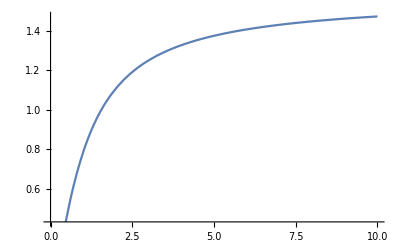

```mathematica
Plot[ I ArcTanh[-I x],{x,0,10}]
```

```mathematica
2  ArcTanh[(m r^2 vesc-√(2 L^2 rE^2+m r^2 (-4 En rE^2+m (r^2-3 rE^2) vesc^2)))/(√2 L rE)]
(%/.r->rE)-2  ArcTanh[0]//Simplify//PowerExpand//Simplify
```

2 ArcTanh[(m r^2 vesc-√(2 L^2 rE^2+m r^2 (-4 En rE^2+m (r^2-3 rE^2) vesc^2)))/(√2 L rE)]

2 ArcTanh[(√2 m rE vesc-2 √(L^2-m rE^2 (2 En+m vesc^2)))/(2 L)]

2/(√(D r^4 (A-C/r^2+B r^2)))

-(2 ArcTan[(√B r^2-√(-C+A r^2+B r^4))/(√C)])/(√C √D)

```mathematica
2 1/(√(D r^4(A+B r^2-C/r^2)))
Integrate[%,r]//Simplify//PowerExpand//Simplify
```

2/(√(D r^4 (A-C/r^2+B r^2)))

-(2 ArcTan[(√B r^2-√(-C+A r^2+B r^4))/(√C)])/(√C √D)

```mathematica
(En-V[r]-L^2/(2 m r^2)/.V[r]->pott)//Simplify
(A+B r^2-C/r^2)/.{D->(2m)/L^2,A->Coefficient[%,r,0],B->Coefficient[%,r,2],C->-Coefficient[%,r,-2]}//Simplify
```

En-L^2/(2 m r^2)-(m (r^2-3 rE^2) vesc^2)/(4 rE^2)

En-L^2/(2 m r^2)-(m (r^2-3 rE^2) vesc^2)/(4 rE^2)

```mathematica
pott
```

(m (r^2-3 rE^2) vesc^2)/(4 rE^2)

```mathematica
(En-V[r]-L^2/(2 m r^2)/.V[r]->pott)//Simplify
-(2 ArcTan[(√B r^2-√(-C+A r^2-B r^4))/(√C)])/(√C √D)/.{D->(2m)/L^2,A->Coefficient[%,r,0],B->Coefficient[%,r,2],C->-Coefficient[%,r,-2]}//Simplify//PowerExpand//Simplify
%/.{vesc->1,m->1,rE->1,En->1000,L->1}/.r->0.1//N
(En-V[r]-L^2/(2 m r^2)/.V[r]->pott)/.{vesc->1,m->1,rE->1,En->1000,L->1}/.r->0.1//N//Simplify
```

En-L^2/(2 m r^2)-(m (r^2-3 rE^2) vesc^2)/(4 rE^2)

-2 ArcTan[(ⅈ m r^2 vesc-√m rE √(-(2 L^2)/m+r^2 (4 En+3 m vesc^2+(m r^2 vesc^2)/rE^2)))/(√2 L rE)]

2.69074-0.000706573 ⅈ

950.748

1/(√2 √(r^4 (1000-1/(2 r^2)+1/4 (3-r^2))))

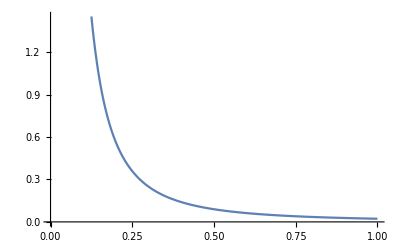

```mathematica
1/(√((2 m r^4)/L^2(En-V[r]-L^2/(2 m r^2)/.V[r]->pott)))/.{vesc->1,m->1,rE->1,En->1000,L->1}
Plot[%,{r,0,1}]
```

```mathematica
D[ArcTan[x],x]
```

1/(1+x^2)

```mathematica
1/(√(D r^4(A+B r^2-C/r^2)))//Simplify//PowerExpand//Simplify
```

1/(√D r √(-C+A r^2+B r^4))

```mathematica
pott=-m((rE vesc^2/2)/(2 rE^3))( 3 rE^2-r^2)(*-α/r*)//Simplify
(En-V[r]-L^2/(2 m r^2)/.V[r]->pott)//Simplify
coeffrepl={D->(2m)/L^2,A->Coefficient[%,r,2],B->Coefficient[%,r,0],C->Coefficient[%,r,-2]}//Simplify
1/r^2(C+B r^2+A r^4)/.coeffrepl//Simplify
```

(m (r^2-3 rE^2) vesc^2)/(4 rE^2)

En-L^2/(2 m r^2)-(m (r^2-3 rE^2) vesc^2)/(4 rE^2)

{D→(2 m)/L^2,A→-(m vesc^2)/(4 rE^2),B→En+(3 m vesc^2)/4,C→-L^2/(2 m)}

En-L^2/(2 m r^2)-(m (r^2-3 rE^2) vesc^2)/(4 rE^2)

```mathematica
coeffrepl
```

{D→(2 m)/L^2,A→-(m vesc^2)/(4 rE^2),B→En+(3 m vesc^2)/4,C→-L^2/(2 m)}

```mathematica
C+B r^2+A r^4
A(r^2+B/(2 A))^2+C-B^2/(4 A)
%//Expand
1/(r √D √(%%))
1/(2 r)%/.r->x^(1/2)
Integrate[%,x]
Solve[0==C+B r^2+A r^4/.r->x^(1/2),x][[1]]
%%/.%//Simplify
%%/.coeffrepl//Simplify//PowerExpand//Simplify
%%/.coeffrepl//Simplify//PowerExpand//Simplify
%%%%%/.r->rE/.coeffrepl//Simplify//PowerExpand//Simplify
```

C+B r^2+A r^4

-B^2/(4 A)+C+A (B/(2 A)+r^2)^2

C+B r^2+A r^4

1/(√D r √(-B^2/(4 A)+C+A (B/(2 A)+r^2)^2))

1/(2 √D x √(-B^2/(4 A)+C+A (B/(2 A)+x)^2))

ArcTanh[(√A x-√(C+x (B+A x)))/(√C)]/(√C √D)

{x→(-B+√(B^2-4 A C))/(2 A)}

ArcTanh[(-B+√(B^2-4 A C))/(2 √A √C)]/(√C √D)

{x→(rE^2 (4 En+3 m vesc^2-4 √(-(L^2 vesc^2)/(2 rE^2)+(En+(3 m vesc^2)/4)^2)))/(2 m vesc^2)}

ⅈ ArcTanh[(√2 rE (-En-(3 m vesc^2)/4+√(-(L^2 vesc^2)/(2 rE^2)+(En+(3 m vesc^2)/4)^2)))/(L vesc)]

-ArcTan[(ⅈ m vesc x-√m rE √(-(2 L^2)/m+4 En x+m vesc^2 x (3-x/rE^2)))/(√2 L rE)]

```mathematica
dr==D[1/x,x]dx
```

dr==-dx/x^2

```mathematica
I ArcTan[-100]//N
```

0.-1.5608 ⅈ

```mathematica
1/(√D r √(-B^2/(4 A)+C+A (B/(2 A)+r^2)^2))
Integrate[%,r]
```

1/(√D r √(-B^2/(4 A)+C+A (B/(2 A)+r^2)^2))

ArcTanh[(√A r^2-√(C+B r^2+A r^4))/(√C)]/(√C √D)

```mathematica
C+B r^2+A r^4
A(r^2+B/(2 A))^2+C-B^2/(4 A)
%//Expand
1/(r √D √(%%))
r^2%/.r->1/x
Integrate[%,x]
Solve[0==C+B r^2+A r^4/.r->x^(1/2),x][[1]]
%%/.%//Simplify
%%/.coeffrepl//Simplify//PowerExpand//Simplify
%%/.coeffrepl//Simplify//PowerExpand//Simplify
%%%%%/.r->rE/.coeffrepl//Simplify//PowerExpand//Simplify
```

C+B r^2+A r^4

-B^2/(4 A)+C+A (B/(2 A)+r^2)^2

C+B r^2+A r^4

1/(√D r √(-B^2/(4 A)+C+A (B/(2 A)+r^2)^2))

1/(√D √(-B^2/(4 A)+C+A (B/(2 A)+1/x^2)^2) x)

-(√(A+B x^2+C x^4) Log[B+2 C x^2-2 √C √(A+B x^2+C x^4)])/(2 √C √D x^2 √(C+(A+B x^2)/x^4))

{x→(-B+√(B^2-4 A C))/(2 A)}

-((2 A^2 √(A+(B (B-√(B^2-4 A C))^2)/(4 A^2)+(C (B-√(B^2-4 A C))^4)/(16 A^4)) Log[B+(C (B-√(B^2-4 A C))^2)/(2 A^2)-2 √C √(A+(B (B-√(B^2-4 A C))^2)/(4 A^2)+(C (B-√(B^2-4 A C))^4)/(16 A^4))])/(√C (B-√(B^2-4 A C))^2 √(C+(16 A^4 (A+(B (B-√(B^2-4 A C))^2)/(4 A^2)))/((B-√(B^2-4 A C))^4)) √D))

{x→(rE^2 (4 En+3 m vesc^2-4 √(-(L^2 vesc^2)/(2 rE^2)+(En+(3 m vesc^2)/4)^2)))/(2 m vesc^2)}

(ⅈ m^2 vesc^4 √(-(m vesc^2)/(4 rE^2)+(4 rE^4 (En+(3 m vesc^2)/4) (En+(3 m vesc^2)/4-√(-(L^2 vesc^2)/(2 rE^2)+(En+(3 m vesc^2)/4)^2))^2)/(m^2 vesc^4)-(8 L^2 rE^8 (En+(3 m vesc^2)/4-√(-(L^2 vesc^2)/(2 rE^2)+(En+(3 m vesc^2)/4)^2))^4)/(m^5 vesc^8)) Log[En+(3 m vesc^2)/4-(4 L^2 rE^4 (En+(3 m vesc^2)/4-√(-(L^2 vesc^2)/(2 rE^2)+(En+(3 m vesc^2)/4)^2))^2)/(m^3 vesc^4)-1/(√m)ⅈ L √(-(m vesc^2)/(2 rE^2)+(8 rE^4 (En+(3 m vesc^2)/4) (En+(3 m vesc^2)/4-√(-(L^2 vesc^2)/(2 rE^2)+(En+(3 m vesc^2)/4)^2))^2)/(m^2 vesc^4)-(16 L^2 rE^8 (En+(3 m vesc^2)/4-√(-(L^2 vesc^2)/(2 rE^2)+(En+(3 m vesc^2)/4)^2))^4)/(m^5 vesc^8))])/(8 rE^4 (En+(3 m vesc^2)/4-√(-(L^2 vesc^2)/(2 rE^2)+(En+(3 m vesc^2)/4)^2))^2 √(-L^2/(2 m)-(4 m^5 vesc^10)/(rE^10 (4 En+3 m vesc^2-4 √(-(L^2 vesc^2)/(2 rE^2)+(En+(3 m vesc^2)/4)^2))^4)+(m^2 vesc^4 (4 En+3 m vesc^2))/(rE^4 (4 En+3 m vesc^2-4 √(-(L^2 vesc^2)/(2 rE^2)+(En+(3 m vesc^2)/4)^2))^2)))

(ⅈ √(4 En x^2-(2 L^2 x^4)/m+(m vesc^2 (-1+3 rE^2 x^2))/rE^2) Log[En+(3 m vesc^2)/4-(L^2 x^2)/m-(ⅈ L √(-(m vesc^2)/rE^2+4 En x^2+3 m vesc^2 x^2-(2 L^2 x^4)/m))/(√2 √m)])/(2 x^2 √(-(2 L^2)/m+(4 En)/x^2+(m vesc^2 (-1+3 rE^2 x^2))/(rE^2 x^4)))

```mathematica
pott=(*-m((rE vesc^2/2)/(2 rE^3))( 3 rE^2-r^2)*)-α/r//Simplify
(En-V[r]-L^2/(2 m r^2)/.V[r]->pott)//Simplify
(*Solve[%==0,r](*[[4]]*)*)
2 1/(√((2 m r^4)/L^2(En-V[r]-L^2/(2 m r^2))))/.V[r]->pott//Simplify
Integrate[%,r(*,{r,rmin,rE},Assumptions->En-pott-L^2/(2 m r^2)>0*)]//Simplify//PowerExpand//Simplify
```

-α/r

En-L^2/(2 m r^2)+α/r

2/(√(r^2 (-1+(2 m r (En r+α))/L^2)))

-4 ArcTan[(√2 √En √m r)/L-√(-1+(2 m r (En r+α))/L^2)]

```mathematica
Cos[-ArcTan[(√2 √En √m r)/L-√(-1+(2 m r (En r+α))/L^2)]]//FullSimplify
```

1/(√(1+(-(√2 √En √m r)/L+√(-1+(2 m r (En r+α))/L^2))^2))

```mathematica
pott=-m((rE vesc^2/2)/(2 rE^3))( 3 rE^2-r^2)(*-α/r*)//Simplify
(En-V[r]-L^2/(2 m r^2)/.V[r]->pott)//Simplify
(*Solve[%==0,r](*[[4]]*)*)
2 1/(√((2 m r^4)/L^2(En-V[r]-L^2/(2 m r^2))))/.V[r]->pott//Simplify
Integrate[%,r(*,{r,rmin,rE},Assumptions->En-pott-L^2/(2 m r^2)>0*),Assumptions->r>0]//Simplify//PowerExpand//Simplify
```

(m (r^2-3 rE^2) vesc^2)/(4 rE^2)

En-L^2/(2 m r^2)-(m (r^2-3 rE^2) vesc^2)/(4 rE^2)

2/(√(-r^2+(m r^4 (4 En rE^2-m (r^2-3 rE^2) vesc^2))/(2 L^2 rE^2)))

(2 r √(2 L^2 rE^2+m r^2 (-4 En rE^2+m (r^2-3 rE^2) vesc^2)) ArcTanh[(m r^2 vesc-√(2 L^2 rE^2+m r^2 (-4 En rE^2+m (r^2-3 rE^2) vesc^2)))/(√2 L rE)])/(L rE √(-2 r^2+(m r^4 (4 En rE^2-m (r^2-3 rE^2) vesc^2))/(L^2 rE^2)))

```mathematica
pott=-m((rE vesc^2/2)/(2 rE^3))( 3 rE^2-r^2)(*-α/r*)//Simplify
(En-V[r]-L^2/(2 m r^2)/.V[r]->pott)//Simplify
(*coeffrepl={D->(2m)/L^2,A->Coefficient[%,r,2],B->Coefficient[%,r,0],C->Coefficient[%,r,-2]}//Simplify*)
coeffrepl={D->(2m)/L^2,A->-Coefficient[%,r,2],B->Coefficient[%,r,0],C->-Coefficient[%,r,-2]}//Simplify
1/r^2(C+B r^2+A r^4)/.coeffrepl//Simplify
```

(m (r^2-3 rE^2) vesc^2)/(4 rE^2)

En-L^2/(2 m r^2)-(m (r^2-3 rE^2) vesc^2)/(4 rE^2)

{D→(2 m)/L^2,A→(m vesc^2)/(4 rE^2),B→En+(3 m vesc^2)/4,C→L^2/(2 m)}

En+L^2/(2 m r^2)+(m (r^2+3 rE^2) vesc^2)/(4 rE^2)

```mathematica
C+B r^2+A r^4/.A->-A/.C->-C
A(r^2+B/(2 A))^2+C-B^2/(4 A)/.A->-A/.C->-C
%//Expand
dr/(r √D √(%%))/.dr->dx D[x^(1/2),x]/.r->x^(1/2) 
(*x/.Solve[s==(B/(2 A)+x)^2,x][[2]]
%%/.dx->ds D[%,s]/.x->%//Simplify*)

%/.x->x-B/(2A)
(*Solve[1/(√(-B^2/(4 A)+C+A x^2))+R/(-B/(2 A)+x)==1/((-B/(2 A)+x) √(-B^2/(4 A)+C+A x^2)),R]
1/(√(-B^2/(4 A)+C+A x^2))+R/(-B/(2 A)+x)/.%[[1]]*)
Assuming[{0<A(r^2+B/(2 A))^2+C-B^2/(4 A)/.r->x^(1/2) /.x->x-B/(2A)//Simplify,A>0,D>0,C>0,B>0},Integrate[%/dx,x]]//Simplify//PowerExpand//Simplify
Solve[0==(A(r^2+B/(2 A))^2+C-B^2/(4 A)/.r->x^(1/2) /.x->x-B/(2A)),x][[2]]
%%/.%//Simplify(*//TrigToExp//Simplify*)//PowerExpand//Simplify
%/.coeffrepl//Simplify//PowerExpand//Simplify

(*%/.coeffrepl//Simplify//PowerExpand*)
```

-C+B r^2-A r^4

B^2/(4 A)-C-A (-B/(2 A)+r^2)^2

-C+B r^2-A r^4

dx/(2 √D x √(B^2/(4 A)-C-A (-B/(2 A)+x)^2))

dx/(2 √D (-B/(2 A)+x) √(B^2/(4 A)-C-A (-B/A+x)^2))

ArcTan[(-B^2-4 A C+2 A B x)/(2 A √C √(-(3 B^2)/A-4 C+8 B x-4 A x^2))]/(2 √C √D)

{x→(√(B^2-4 A C))/(2 A)}

ArcTan[(-B^2-4 A C+B √(B^2-4 A C))/(4 √A √B √C √(-B+√(B^2-4 A C)))]/(2 √C √D)

1/2 ArcTan[(rE (-(L^2 vesc^2)/(2 rE^2)-(En+(3 m vesc^2)/4)^2+(En+(3 m vesc^2)/4) √(-(L^2 vesc^2)/(2 rE^2)+(En+(3 m vesc^2)/4)^2)))/(√2 L vesc √(En+(3 m vesc^2)/4) √(-En-(3 m vesc^2)/4+√(-(L^2 vesc^2)/(2 rE^2)+(En+(3 m vesc^2)/4)^2)))]

```mathematica
Integrate[1/((x+α^2)√(x^2+β^2)),x]
Integrate[1/((x-α^2)√(x^2-β^2)),x]
Integrate[1/((x-α^2)√(x^2+β^2)),x]
Integrate[1/((x+α^2)√(x^2-β^2)),x]
```

-(2 ArcTan[(x+α^2-√(x^2+β^2))/(√(-α^4-β^2))])/(√(-α^4-β^2))

-(2 ArcTan[(x-α^2-√(x^2-β^2))/(√(-α^4+β^2))])/(√(-α^4+β^2))

-(2 ArcTan[(x-α^2-√(x^2+β^2))/(√(-α^4-β^2))])/(√(-α^4-β^2))

-(2 ArcTan[(x+α^2-√(x^2-β^2))/(√(-α^4+β^2))])/(√(-α^4+β^2))

#### The distribution at the surface - assuming point like Earth

```mathematica
VE
```

{30,0,0}

```mathematica
4 π v^2 nF/(((2 π)/3 v0^2)^(3/2))E^(- 3/(2 v0^2)(v^2-vesc^2))
```

(3 ⅇ^(-(3 (v^2-vesc^2))/(2 v0^2)) nF √(6/π) v^2)/((v0^2)^(3/2))

```mathematica
distatEarth(*/.{v->(*v/(√(#.#))*)#&@{vx,vy,vz},rh->#/(√(#.#))&@{rx,ry,rz}}*)/.vesc->0/.vE->0//Simplify//FullSimplify
Integrate[4 π v^2%,{v,0,∞}]//PowerExpand
```

(3 √(3/2) ⅇ^(-(3 v^2)/(2 v0^2)) nF)/(2 π^(3/2) (v0^2)^(3/2))

ConditionalExpression[nF, Re[v0^2]>0]

```mathematica
"We want the number density, which means integrating over all v>vesc and looking at various positions in the Earth. We can integrate over v numerically"
distatEarth
"we can impose v > vesc with a Boole"
(*nofrhatrE[rxt_,ryt_,rzt_]:=NIntegrate[distatEarth Boole[√(vx^2+vy^2+vz^2)>vesc]/.{rx->rxt,ry->ryt,rz->rzt}/.{v0->20,vesc->11,nF->1}/.v->√(vx^2+vy^2+vz^2),{vx,0,∞},{vy,0,∞},{vz,0,∞},MinRecursion->9]*)
(*nofrhatrE[rxt_,ryt_,rzt_,v0t_:20,vEt_:30]:=NIntegrate[distatEarth Boole[√(vx^2+vy^2+vz^2)>vesc]/.{rx->rxt,ry->ryt,rz->rzt}/.{v0->vEt,vE->vEt,vesc->11,nF->1}/.v->√(vx^2+vy^2+vz^2),{vx,0,∞},{vy,0,∞},{vz,0,∞},MinRecursion->9,PrecisionGoal->5]*)
Clear[nofrhatrE]
nofrhatrE[rxt_,ryt_,rzt_,v0t_:20,vEt_:30,vesct_:11]:=NIntegrate[vm^2 Sin[ψ]distatEarth /.{rx->rxt,ry->ryt,rz->rzt}/.{v0->v0t,vE->vEt,vesc->vesct,nF->1}/.v->√(vx^2+vy^2+vz^2)/.{vx->vm Sin[ψ]Cos[ϕ],vy->vm  Sin[ψ]Sin[ϕ],vz->vm  Cos[ψ]},{vm,vesct,∞},{ψ,0,π},{ϕ,0,2 π},MinRecursion->9,PrecisionGoal->5,Method->"LocalAdaptive"]
```

We want the number density, which means integrating over all v>vesc and looking at various positions in the Earth. We can integrate over v numerically

1/(2 π^(3/2) (v0^2)^(3/2))3 √(3/2) ⅇ^(-(3 (((2 v vy (-rx v √(v^2-vesc^2) vx-rz v √(v^2-vesc^2) vz+√(rx^2+ry^2+rz^2) (v^2-vesc^2) √(vx^2+vy^2+vz^2))+ry √(v^2-vesc^2) (-2 v^2 vy^2+vesc^2 (vx^2+vy^2+vz^2)))^2)/((vx^2+vy^2+vz^2) (2 rx v √(v^2-vesc^2) vx+2 ry v √(v^2-vesc^2) vy+2 rz v √(v^2-vesc^2) vz-2 √(rx^2+ry^2+rz^2) v^2 √(vx^2+vy^2+vz^2)+√(rx^2+ry^2+rz^2) vesc^2 √(vx^2+vy^2+vz^2))^2)+((2 v vz (-rx v √(v^2-vesc^2) vx-ry v √(v^2-vesc^2) vy+√(rx^2+ry^2+rz^2) (v^2-vesc^2) √(vx^2+vy^2+vz^2))+rz √(v^2-vesc^2) (-2 v^2 vz^2+vesc^2 (vx^2+vy^2+vz^2)))^2)/((vx^2+vy^2+vz^2) (2 rx v √(v^2-vesc^2) vx+2 ry v √(v^2-vesc^2) vy+2 rz v √(v^2-vesc^2) vz-2 √(rx^2+ry^2+rz^2) v^2 √(vx^2+vy^2+vz^2)+√(rx^2+ry^2+rz^2) vesc^2 √(vx^2+vy^2+vz^2))^2)+(vE+(2 v vx (-ry v √(v^2-vesc^2) vy-rz v √(v^2-vesc^2) vz+√(rx^2+ry^2+rz^2) (v^2-vesc^2) √(vx^2+vy^2+vz^2))+rx √(v^2-vesc^2) (-2 v^2 vx^2+vesc^2 (vx^2+vy^2+vz^2)))/(√(vx^2+vy^2+vz^2) (2 rx v √(v^2-vesc^2) vx+2 ry v √(v^2-vesc^2) vy+2 rz v √(v^2-vesc^2) vz-2 √(rx^2+ry^2+rz^2) v^2 √(vx^2+vy^2+vz^2)+√(rx^2+ry^2+rz^2) vesc^2 √(vx^2+vy^2+vz^2))))^2))/(2 v0^2)) nF

we can impose v > vesc with a Boole

We choose θ to parametrize the angle in the x-y plane (θ = 0 corresponds to the point where you are on the surface in the direction opposite of the Earth’s motion on the surface), we use the axis

```mathematica
nofrhatrE[Cos[π/2],Sin[π/2],0,20,30]
nofrhatrE[Cos[π/2],Sin[π/2],0,220,230]
```

0.36602

0.35583

```mathematica
nstabledisk=Monitor[Quiet@Table[{π θ,nofrhatrE[Cos[π θ],Sin[π θ],0,20,30]},{θ,0,1,0.1}],θ]
nstablehalo=Monitor[Quiet@Table[{π θ,nofrhatrE[Cos[π θ],Sin[π θ],0,220,230]},{θ,0,1,0.1}],θ]
nstabledisknovE=Monitor[Quiet@Table[{π θ,nofrhatrE[Cos[π θ],Sin[π θ],0,20,0]},{θ,0,1,0.1}],θ]
nstablehalonovE=Monitor[Quiet@Table[{π θ,nofrhatrE[Cos[π θ],Sin[π θ],0,220,0]},{θ,0,1,0.1}],θ]
```

{{0.,1.57448},{0.314159,1.4439},{0.628319,1.22822},{0.942478,1.10037},{1.25664,1.04689},{1.5708,1.02556},{1.88496,1.01612},{2.19911,1.01163},{2.51327,1.00943},{2.82743,1.00829},{3.14159,1.00794}}

{{0.,1.00853},{0.314159,1.00747},{0.628319,1.00534},{0.942478,1.00363},{1.25664,1.00259},{1.5708,1.00219},{1.88496,1.00195},{2.19911,1.00183},{2.51327,1.00175},{2.82743,1.00173},{3.14159,1.00173}}

{{0.,1.29653},{0.314159,1.29653},{0.628319,1.29653},{0.942478,1.29653},{1.25664,1.29653},{1.5708,1.29653},{1.88496,1.29653},{2.19911,1.29653},{2.51327,1.29653},{2.82743,1.29653},{3.14159,1.29653}}

{{0.,1.00306},{0.314159,1.00306},{0.628319,1.00306},{0.942478,1.00306},{1.25664,1.00306},{1.5708,1.00306},{1.88496,1.00306},{2.19911,1.00306},{2.51327,1.00306},{2.82743,1.00306},{3.14159,1.00306}}

So we can see that there is clear inhomogeneity but it is small and only present for the disk case

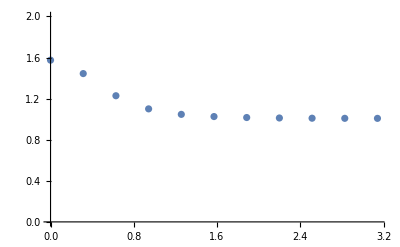

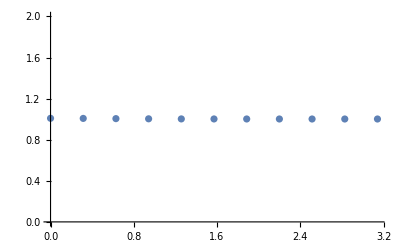

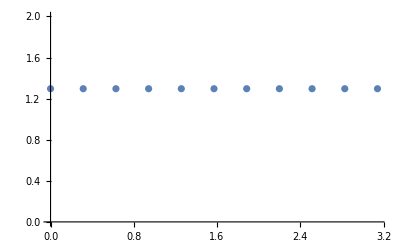

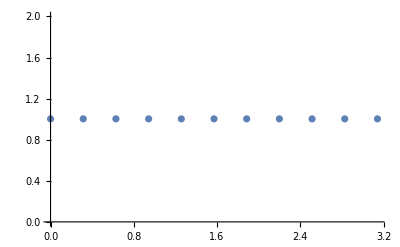

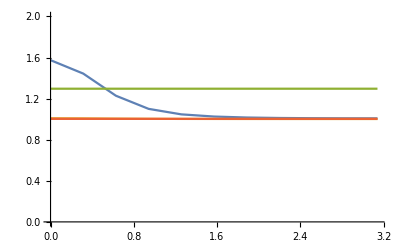

```mathematica
"So we can see that there is clear inhomogeneity but it is small and only present for the disk case"
ListPlot[nstabledisk,PlotRange->{0,2}]
ListPlot[nstablehalo,PlotRange->{0,2}]
ListPlot[nstabledisknovE,PlotRange->{0,2}]
ListPlot[nstablehalonovE,PlotRange->{0,2}]
ListLinePlot[{nstabledisk,nstablehalo,nstabledisknovE,nstablehalonovE},PlotRange->{0,2}]
```

```mathematica
"Note that this implies that in the disk case, in the absence of any capture, we can expect daily modulations on the order of a factor of 1/2 in the incoming flux"
```

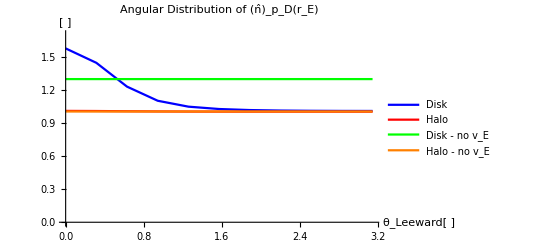

```mathematica
ListLinePlot[{nstabledisk,nstablehalo,nstabledisknovE,nstablehalonovE},(*PlotRange->{0,2},*)PlotStyle->#,PlotLegends->LineLegend[#,{"Disk","Halo","Disk - no v_E","Halo - no v_E"}],PlotLabel->"Angular Distribution of (n̂)_p_D(r_E)",AxesLabel->{"θ_Leeward[ ]","[ ]"},PlotRange->{0,1.7}]&@{Blue,Red,Green,Orange}
```

```mathematica
nstabledisknovEnovesc=Monitor[Quiet@Table[{π θ,nofrhatrE[Cos[π θ],Sin[π θ],0,20,0,0]},{θ,0,1,0.1}],θ]
```

{{0.,0.353659},{0.314159,0.353659},{0.628319,0.353659},{0.942478,0.353659},{1.25664,0.353659},{1.5708,0.353659},{1.88496,0.353659},{2.19911,0.353659},{2.51327,0.353659},{2.82743,0.353659},{3.14159,0.353659}}

```mathematica
"We should also plot the speed disributions as a function of position as a contour plot. so we can see the effect this will have for capture etc."
```

```mathematica
((rE vesc^2/2)/(2 rE^3))( 3 rE^2-r^2)/.r->{rE,0}
3/2(11/20)^2//N
3/2 3/2(11/20)^2//N
```

{vesc^2/2,(3 vesc^2)/4}

0.45375

0.680625

```mathematica
Clear[nofrhfnofvm]
nofrhfnofvm[vm_?NumericQ,rxt_,ryt_,rzt_,v0t_:20,vEt_:30,vesct_:11]:=NIntegrate[vm^2 Sin[ψ]distatEarth /.{rx->rxt,ry->ryt,rz->rzt}/.{v0->v0t,vE->vEt,vesc->vesct,nF->1}/.v->√(vx^2+vy^2+vz^2)/.{vx->vm Sin[ψ]Cos[ϕ],vy->vm  Sin[ψ]Sin[ϕ],vz->vm  Cos[ψ]},{ψ,0,π},{ϕ,0,2 π},MinRecursion->9,PrecisionGoal->5,Method->"LocalAdaptive"]
```

```mathematica
nstablediskfnofvm=Monitor[Quiet@Table[{vm,π θ,nofrhfnofvm[vm,Cos[π θ],Sin[π θ],0,20,30,11]},{θ,0,1,0.1},{vm,11,61,5}],{vm,θ}]
```

{{{11,0.,0.00214572},{16,0.,0.0113616},{21,0.,0.0261433},{26,0.,0.0438446},{31,0.,0.0571149},{36,0.,0.0592751},{41,0.,0.0496476},{46,0.,0.0338131},{51,0.,0.0188146},{56,0.,0.00858054},{61,0.,0.00321452}},{{11,0.314159,0.00214572},{16,0.314159,0.0108665},{21,0.314159,0.0245681},{26,0.314159,0.0406962},{31,0.314159,0.052517},{36,0.314159,0.0541021},{41,0.314159,0.0450496},{46,0.314159,0.0305387},{51,0.314159,0.0169293},{56,0.314159,0.007698},{61,0.314159,0.00287728}},{{11,0.628319,0.00214572},{16,0.628319,0.00966615},{21,0.628319,0.0211369},{26,0.628319,0.0344748},{31,0.628319,0.0442371},{36,0.628319,0.0455895},{41,0.628319,0.0381201},{46,0.628319,0.0260104},{51,0.628319,0.0145334},{56,0.628319,0.00666579},{61,0.628319,0.00251376}},{{11,0.942478,0.00214572},{16,0.942478,0.0083297},{21,0.942478,0.0180032},{26,0.942478,0.029726},{31,0.942478,0.038907},{36,0.942478,0.0409401},{41,0.942478,0.0348944},{46,0.942478,0.0242068},{51,0.942478,0.0137144},{56,0.942478,0.00636201},{61,0.942478,0.00242137}},{{11,1.25664,0.00214572},{16,1.25664,0.00725318},{21,1.25664,0.0160524},{26,1.25664,0.0273744},{31,1.25664,0.0367717},{36,1.25664,0.0394141},{41,1.25664,0.0340165},{46,1.25664,0.023795},{51,1.25664,0.0135557},{56,1.25664,0.0063114},{61,1.25664,0.00240798}},{{11,1.5708,0.00214572},{16,1.5708,0.006531},{21,1.5708,0.0150587},{26,1.5708,0.0264238},{31,1.5708,0.0360642},{36,1.5708,0.0389863},{41,1.5708,0.0338021},{46,1.5708,0.0237048},{51,1.5708,0.0135235},{56,1.5708,0.0063017},{61,1.5708,0.00240549}},{{11,1.88496,0.00214572},{16,1.88496,0.00609213},{21,1.88496,0.0145892},{26,1.88496,0.0260513},{31,1.88496,0.0358214},{36,1.88496,0.0388516},{41,1.88496,0.0337376},{46,1.88496,0.023678},{51,1.88496,0.013514},{56,1.88496,0.00629712},{61,1.88496,0.00240429}},{{11,2.19911,0.00214572},{16,2.19911,0.0058381},{21,2.19911,0.0143666},{26,2.19911,0.0258951},{31,2.19911,0.0357257},{36,2.19911,0.0387995},{41,2.19911,0.0337126},{46,2.19911,0.0236582},{51,2.19911,0.0135067},{56,2.19911,0.00629652},{61,2.19911,0.00240413}},{{11,2.51327,0.00214572},{16,2.51327,0.00569665},{21,2.51327,0.0142589},{26,2.51327,0.0258243},{31,2.51327,0.0356832},{36,2.51327,0.0387763},{41,2.51327,0.0337013},{46,2.51327,0.0236628},{51,2.51327,0.0135059},{56,2.51327,0.00629627},{61,2.51327,0.00240406}},{{11,2.82743,0.00214572},{16,2.82743,0.00562552},{21,2.82743,0.0142092},{26,2.82743,0.0257926},{31,2.82743,0.0356641},{36,2.82743,0.0387658},{41,2.82743,0.0336962},{46,2.82743,0.0236586},{51,2.82743,0.0135056},{56,2.82743,0.00629613},{61,2.82743,0.00240403}},{{11,3.14159,0.00214572},{16,3.14159,0.00560387},{21,3.14159,0.0141946},{26,3.14159,0.0257834},{31,3.14159,0.0356586},{36,3.14159,0.0387628},{41,3.14159,0.0336948},{46,3.14159,0.02366},{51,3.14159,0.0135074},{56,3.14159,0.00629677},{61,3.14159,0.0024042}}}

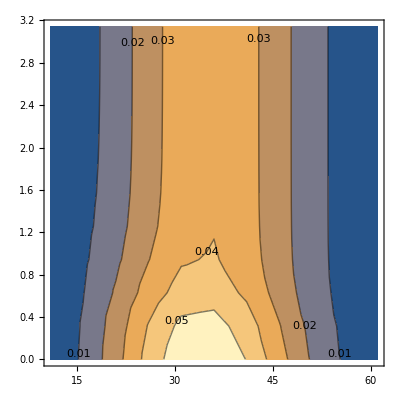

```mathematica
ListContourPlot[Flatten[nstablediskfnofvm,1],ContourLabels->All]
```

```mathematica
nstablediskfnofvmnovesc=Monitor[Quiet@Table[{vm,π θ,nofrhfnofvm[vm,Cos[π θ],Sin[π θ],0,20,30,0]},{θ,0,1,0.1},{vm,11,61,5}],{vm,θ}]
nstablediskfnofvmnovescnovE=Monitor[Quiet@Table[{vm,π θ,nofrhfnofvm[vm,Cos[π θ],Sin[π θ],0,20,0,0]},{θ,0,1,0.1},{vm,11,61,5}],{vm,θ}]
nstablediskfnofvmnovE=Monitor[Quiet@Table[{vm,π θ,nofrhfnofvm[vm,Cos[π θ],Sin[π θ],0,20,0,11]},{θ,0,1,0.1},{vm,11,61,5}],{vm,θ}]
```

{{{11,0.,0.00324862},{16,0.,0.00882894},{21,0.,0.0178479},{26,0.,0.0281989},{31,0.,0.0355674},{36,0.,0.0362236},{41,0.,0.0299945},{46,0.,0.020284},{51,0.,0.0112376},{56,0.,0.00511177},{61,0.,0.00191232}},{{11,0.314159,0.00324862},{16,0.314159,0.00882894},{21,0.314159,0.0178479},{26,0.314159,0.0281989},{31,0.314159,0.0355674},{36,0.314159,0.0362236},{41,0.314159,0.0299945},{46,0.314159,0.020284},{51,0.314159,0.0112376},{56,0.314159,0.00511177},{61,0.314159,0.00191232}},{{11,0.628319,0.00324862},{16,0.628319,0.00882894},{21,0.628319,0.0178479},{26,0.628319,0.0281989},{31,0.628319,0.0355674},{36,0.628319,0.0362236},{41,0.628319,0.0299945},{46,0.628319,0.020284},{51,0.628319,0.0112376},{56,0.628319,0.00511177},{61,0.628319,0.00191232}},{{11,0.942478,0.00324862},{16,0.942478,0.00882894},{21,0.942478,0.0178479},{26,0.942478,0.0281989},{31,0.942478,0.0355674},{36,0.942478,0.0362236},{41,0.942478,0.0299945},{46,0.942478,0.020284},{51,0.942478,0.0112376},{56,0.942478,0.00511177},{61,0.942478,0.00191232}},{{11,1.25664,0.00324862},{16,1.25664,0.00882894},{21,1.25664,0.0178479},{26,1.25664,0.0281989},{31,1.25664,0.0355674},{36,1.25664,0.0362236},{41,1.25664,0.0299945},{46,1.25664,0.020284},{51,1.25664,0.0112376},{56,1.25664,0.00511177},{61,1.25664,0.00191232}},{{11,1.5708,0.00324862},{16,1.5708,0.00882894},{21,1.5708,0.0178479},{26,1.5708,0.0281989},{31,1.5708,0.0355674},{36,1.5708,0.0362236},{41,1.5708,0.0299945},{46,1.5708,0.020284},{51,1.5708,0.0112376},{56,1.5708,0.00511177},{61,1.5708,0.00191232}},{{11,1.88496,0.00324862},{16,1.88496,0.00882894},{21,1.88496,0.0178479},{26,1.88496,0.0281989},{31,1.88496,0.0355674},{36,1.88496,0.0362236},{41,1.88496,0.0299945},{46,1.88496,0.020284},{51,1.88496,0.0112376},{56,1.88496,0.00511177},{61,1.88496,0.00191232}},{{11,2.19911,0.00324862},{16,2.19911,0.00882894},{21,2.19911,0.0178479},{26,2.19911,0.0281989},{31,2.19911,0.0355674},{36,2.19911,0.0362236},{41,2.19911,0.0299945},{46,2.19911,0.020284},{51,2.19911,0.0112376},{56,2.19911,0.00511177},{61,2.19911,0.00191232}},{{11,2.51327,0.00324862},{16,2.51327,0.00882894},{21,2.51327,0.0178479},{26,2.51327,0.0281989},{31,2.51327,0.0355674},{36,2.51327,0.0362236},{41,2.51327,0.0299945},{46,2.51327,0.020284},{51,2.51327,0.0112376},{56,2.51327,0.00511177},{61,2.51327,0.00191232}},{{11,2.82743,0.00324862},{16,2.82743,0.00882894},{21,2.82743,0.0178479},{26,2.82743,0.0281989},{31,2.82743,0.0355674},{36,2.82743,0.0362236},{41,2.82743,0.0299945},{46,2.82743,0.020284},{51,2.82743,0.0112376},{56,2.82743,0.00511177},{61,2.82743,0.00191232}},{{11,3.14159,0.00324862},{16,3.14159,0.00882894},{21,3.14159,0.0178479},{26,3.14159,0.0281989},{31,3.14159,0.0355674},{36,3.14159,0.0362236},{41,3.14159,0.0299945},{46,3.14159,0.020284},{51,3.14159,0.0112376},{56,3.14159,0.00511177},{61,3.14159,0.00191232}}}

{{{11,0.,0.0398342},{16,0.,0.0507983},{21,0.,0.0437276},{26,0.,0.0277678},{31,0.,0.0135571},{36,0.,0.00520554},{41,0.,0.00159373},{46,0.,0.000392573},{51,0.,0.0000782839},{56,0.,0.0000126942},{61,0.,1.6794×10^-6}},{{11,0.314159,0.0398342},{16,0.314159,0.0507983},{21,0.314159,0.0437276},{26,0.314159,0.0277678},{31,0.314159,0.0135571},{36,0.314159,0.00520554},{41,0.314159,0.00159373},{46,0.314159,0.000392573},{51,0.314159,0.0000782839},{56,0.314159,0.0000126942},{61,0.314159,1.6794×10^-6}},{{11,0.628319,0.0398342},{16,0.628319,0.0507983},{21,0.628319,0.0437276},{26,0.628319,0.0277678},{31,0.628319,0.0135571},{36,0.628319,0.00520554},{41,0.628319,0.00159373},{46,0.628319,0.000392573},{51,0.628319,0.0000782839},{56,0.628319,0.0000126942},{61,0.628319,1.6794×10^-6}},{{11,0.942478,0.0398342},{16,0.942478,0.0507983},{21,0.942478,0.0437276},{26,0.942478,0.0277678},{31,0.942478,0.0135571},{36,0.942478,0.00520554},{41,0.942478,0.00159373},{46,0.942478,0.000392573},{51,0.942478,0.0000782839},{56,0.942478,0.0000126942},{61,0.942478,1.6794×10^-6}},{{11,1.25664,0.0398342},{16,1.25664,0.0507983},{21,1.25664,0.0437276},{26,1.25664,0.0277678},{31,1.25664,0.0135571},{36,1.25664,0.00520554},{41,1.25664,0.00159373},{46,1.25664,0.000392573},{51,1.25664,0.0000782839},{56,1.25664,0.0000126942},{61,1.25664,1.6794×10^-6}},{{11,1.5708,0.0398342},{16,1.5708,0.0507983},{21,1.5708,0.0437276},{26,1.5708,0.0277678},{31,1.5708,0.0135571},{36,1.5708,0.00520554},{41,1.5708,0.00159373},{46,1.5708,0.000392573},{51,1.5708,0.0000782839},{56,1.5708,0.0000126942},{61,1.5708,1.6794×10^-6}},{{11,1.88496,0.0398342},{16,1.88496,0.0507983},{21,1.88496,0.0437276},{26,1.88496,0.0277678},{31,1.88496,0.0135571},{36,1.88496,0.00520554},{41,1.88496,0.00159373},{46,1.88496,0.000392573},{51,1.88496,0.0000782839},{56,1.88496,0.0000126942},{61,1.88496,1.6794×10^-6}},{{11,2.19911,0.0398342},{16,2.19911,0.0507983},{21,2.19911,0.0437276},{26,2.19911,0.0277678},{31,2.19911,0.0135571},{36,2.19911,0.00520554},{41,2.19911,0.00159373},{46,2.19911,0.000392573},{51,2.19911,0.0000782839},{56,2.19911,0.0000126942},{61,2.19911,1.6794×10^-6}},{{11,2.51327,0.0398342},{16,2.51327,0.0507983},{21,2.51327,0.0437276},{26,2.51327,0.0277678},{31,2.51327,0.0135571},{36,2.51327,0.00520554},{41,2.51327,0.00159373},{46,2.51327,0.000392573},{51,2.51327,0.0000782839},{56,2.51327,0.0000126942},{61,2.51327,1.6794×10^-6}},{{11,2.82743,0.0398342},{16,2.82743,0.0507983},{21,2.82743,0.0437276},{26,2.82743,0.0277678},{31,2.82743,0.0135571},{36,2.82743,0.00520554},{41,2.82743,0.00159373},{46,2.82743,0.000392573},{51,2.82743,0.0000782839},{56,2.82743,0.0000126942},{61,2.82743,1.6794×10^-6}},{{11,3.14159,0.0398342},{16,3.14159,0.0507983},{21,3.14159,0.0437276},{26,3.14159,0.0277678},{31,3.14159,0.0135571},{36,3.14159,0.00520554},{41,3.14159,0.00159373},{46,3.14159,0.000392573},{51,3.14159,0.0000782839},{56,3.14159,0.0000126942},{61,3.14159,1.6794×10^-6}}}

{{{11,0.,0.0627072},{16,0.,0.0799669},{21,0.,0.0688362},{26,0.,0.0437123},{31,0.,0.0213416},{36,0.,0.00819458},{41,0.,0.00250886},{46,0.,0.000617991},{51,0.,0.000123235},{56,0.,0.0000199832},{61,0.,2.64372×10^-6}},{{11,0.314159,0.0627072},{16,0.314159,0.0799669},{21,0.314159,0.0688362},{26,0.314159,0.0437123},{31,0.314159,0.0213416},{36,0.314159,0.00819458},{41,0.314159,0.00250886},{46,0.314159,0.000617991},{51,0.314159,0.000123235},{56,0.314159,0.0000199832},{61,0.314159,2.64372×10^-6}},{{11,0.628319,0.0627072},{16,0.628319,0.0799669},{21,0.628319,0.0688362},{26,0.628319,0.0437123},{31,0.628319,0.0213416},{36,0.628319,0.00819458},{41,0.628319,0.00250886},{46,0.628319,0.000617991},{51,0.628319,0.000123235},{56,0.628319,0.0000199832},{61,0.628319,2.64372×10^-6}},{{11,0.942478,0.0627072},{16,0.942478,0.0799669},{21,0.942478,0.0688362},{26,0.942478,0.0437123},{31,0.942478,0.0213416},{36,0.942478,0.00819458},{41,0.942478,0.00250886},{46,0.942478,0.000617991},{51,0.942478,0.000123235},{56,0.942478,0.0000199832},{61,0.942478,2.64372×10^-6}},{{11,1.25664,0.0627072},{16,1.25664,0.0799669},{21,1.25664,0.0688362},{26,1.25664,0.0437123},{31,1.25664,0.0213416},{36,1.25664,0.00819458},{41,1.25664,0.00250886},{46,1.25664,0.000617991},{51,1.25664,0.000123235},{56,1.25664,0.0000199832},{61,1.25664,2.64372×10^-6}},{{11,1.5708,0.0627072},{16,1.5708,0.0799669},{21,1.5708,0.0688362},{26,1.5708,0.0437123},{31,1.5708,0.0213416},{36,1.5708,0.00819458},{41,1.5708,0.00250886},{46,1.5708,0.000617991},{51,1.5708,0.000123235},{56,1.5708,0.0000199832},{61,1.5708,2.64372×10^-6}},{{11,1.88496,0.0627072},{16,1.88496,0.0799669},{21,1.88496,0.0688362},{26,1.88496,0.0437123},{31,1.88496,0.0213416},{36,1.88496,0.00819458},{41,1.88496,0.00250886},{46,1.88496,0.000617991},{51,1.88496,0.000123235},{56,1.88496,0.0000199832},{61,1.88496,2.64372×10^-6}},{{11,2.19911,0.0627072},{16,2.19911,0.0799669},{21,2.19911,0.0688362},{26,2.19911,0.0437123},{31,2.19911,0.0213416},{36,2.19911,0.00819458},{41,2.19911,0.00250886},{46,2.19911,0.000617991},{51,2.19911,0.000123235},{56,2.19911,0.0000199832},{61,2.19911,2.64372×10^-6}},{{11,2.51327,0.0627072},{16,2.51327,0.0799669},{21,2.51327,0.0688362},{26,2.51327,0.0437123},{31,2.51327,0.0213416},{36,2.51327,0.00819458},{41,2.51327,0.00250886},{46,2.51327,0.000617991},{51,2.51327,0.000123235},{56,2.51327,0.0000199832},{61,2.51327,2.64372×10^-6}},{{11,2.82743,0.0627072},{16,2.82743,0.0799669},{21,2.82743,0.0688362},{26,2.82743,0.0437123},{31,2.82743,0.0213416},{36,2.82743,0.00819458},{41,2.82743,0.00250886},{46,2.82743,0.000617991},{51,2.82743,0.000123235},{56,2.82743,0.0000199832},{61,2.82743,2.64372×10^-6}},{{11,3.14159,0.0627072},{16,3.14159,0.0799669},{21,3.14159,0.0688362},{26,3.14159,0.0437123},{31,3.14159,0.0213416},{36,3.14159,0.00819458},{41,3.14159,0.00250886},{46,3.14159,0.000617991},{51,3.14159,0.000123235},{56,3.14159,0.0000199832},{61,3.14159,2.64372×10^-6}}}

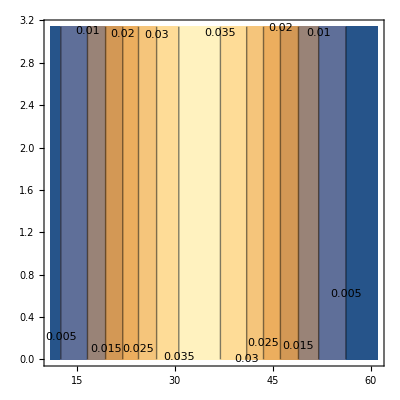

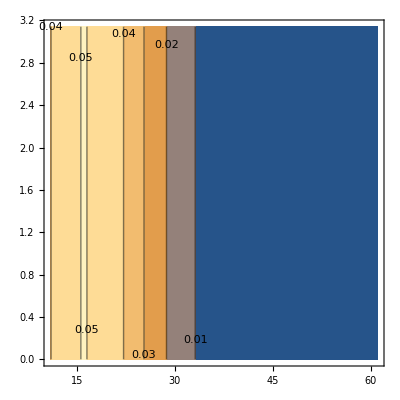

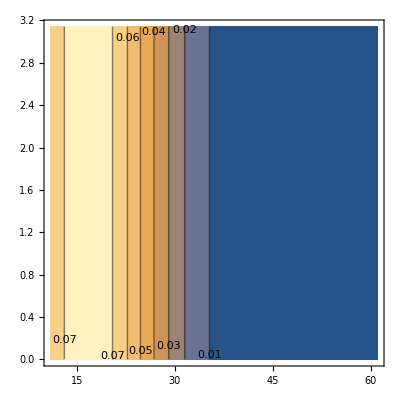

```mathematica
ListContourPlot[Flatten[nstablediskfnofvmnovesc,1],ContourLabels->All]
ListContourPlot[Flatten[nstablediskfnofvmnovescnovE,1],ContourLabels->All]
ListContourPlot[Flatten[nstablediskfnofvmnovE,1],ContourLabels->All]
```

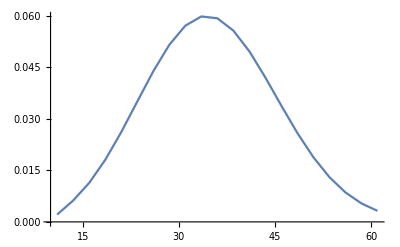

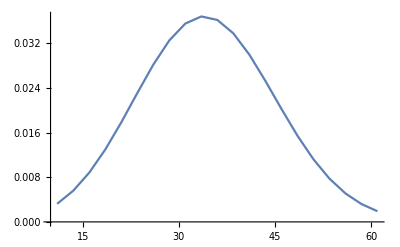

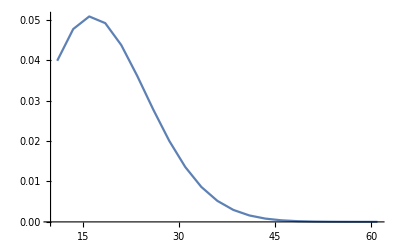

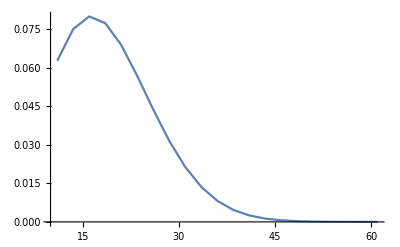

```mathematica
nstablediskfnofvmfixedθ=Monitor[Quiet@Table[{vm,nofrhfnofvm[vm,Cos[π 0],Sin[π 0],0,20,30,11]},{vm,11,61,2.5}],{vm}];
nstablediskfnofvmnovescfixedθ=Monitor[Quiet@Table[{vm,nofrhfnofvm[vm,Cos[π 0],Sin[π 0],0,20,30,0]},{vm,11,61,2.5}],{vm}];
nstablediskfnofvmnovescnovEfixedθ=Monitor[Quiet@Table[{vm,nofrhfnofvm[vm,Cos[π 0],Sin[π 0],0,20,0,0]},{vm,11,61,2.5}],{vm}];
nstablediskfnofvmnovEfixedθ=Monitor[Quiet@Table[{vm,nofrhfnofvm[vm,Cos[π 0],Sin[π 0],0,20,0,11]},{vm,11,61,2.5}],{vm}];
ListLinePlot[nstablediskfnofvmfixedθ]
ListLinePlot[nstablediskfnofvmnovescfixedθ]
ListLinePlot[nstablediskfnofvmnovescnovEfixedθ]
ListLinePlot[nstablediskfnofvmnovEfixedθ]
```

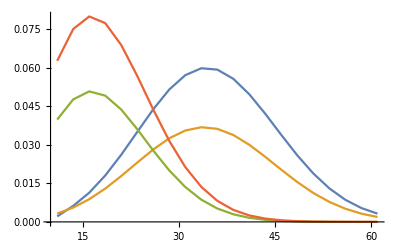

```mathematica
ListLinePlot[{nstablediskfnofvmfixedθ,nstablediskfnofvmnovescfixedθ,nstablediskfnofvmnovescnovEfixedθ,nstablediskfnofvmnovEfixedθ}]
```

```mathematica
nstablediskfnofvmback=Monitor[Quiet@Table[{vm,nofrhfnofvm[vm,Cos[π 0],Sin[π 0],0,20,0,11]},{vm,11,61,2.5}],{vm}];
nstablediskfnofvmfront=Monitor[Quiet@Table[{vm,nofrhfnofvm[vm,Cos[π 1],Sin[π 1],0,20,0,11]},{vm,11,61,2.5}],{vm}];
```

#### Comparison of point mass vs finite sized Earth potentials - and our potential

We would like to use the above results in order to estimate the effect of the inhomogeneity on our potential. 

The above essentially assumes 1/r potential. Both inside the Earth and for some regions in our potential (near rmax) this assumption doesn’t hold.

We would like to compare the potential inside the Earth to a 1/r potential in some way so as to estimate the error in assuming a point mass Earth for the velocity distribution. 

We should also estimate the effect that the debeye drop off has in our potential (hopefully a small one given that this is a small region and it falls off as 1/r or less elsewhere). In the flat potential region, we’ve shown above that this doesn’t matter, regardless of the speed of the Earth, if the escape velocity is 0 there is no inhomogeneity.

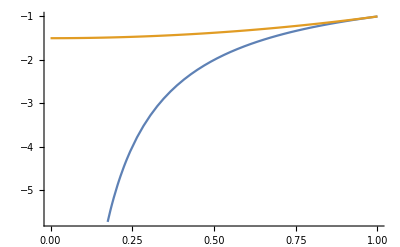

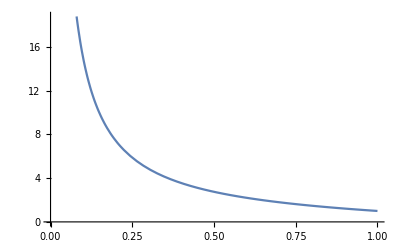

```mathematica
Plot[{-1/r,-1/2(3-r^2)},{r,0,1}]
Plot[{1/r 1/2(3-r^2)},{r,0,1}]
```

```mathematica
"We are at the Earth's surface at r=1 in this plot. We can use this to estimate the solid angle for which the aDM coming from it could be significantly effected significantly. It looks like the disk (Earth's core cross-section) would be of radius 0.8 rE and a distance 0.2 away"
Ωdiff=2 π (1-0.2/(√(0.2^2+0.8^2)))
Ωdiff/(4 π)
"So there is roughly 40% of the solid angle for a point on the surface could vary the number density. Next we need to estimate the change in the angular deflection from such a difference in potential. Both forces are conservative, so the speeds will be identical, it is just a matter of changing where they end up."
```

We are at the Earth's surface at r=1 in this plot. We can use this to estimate the solid angle for which the aDM coming from it could be significantly effected significantly. It looks like the disk (Earth's core cross-section) would be of radius 0.8 rE and a distance 0.2 away

4.75929

0.378732

So there is roughly 40% of the solid angle for a point on the surface could vary the number density. Next we need to estimate the change in the angular deflection from such a difference in potential. Both forces are conservative, so the speeds will be identical, it is just a matter of changing where they end up.

```mathematica
"I think we can also say that the shallower the potential is, the less deflection there will be. Which would mean that the above plots we've made of \hat n would be overestimating the amount of deflection. If we can show that explicitly, we may be able to ignore the inhomogeneity altogether even in the disk case."
```

I think we can also say that the shallower the potential is, the less deflection there will be. Which would mean that the above plots we've made of \hat n would be overestimating the amount of deflection. If we can show that explicitly, we may be able to ignore the inhomogeneity altogether even in the disk case.

#### Fradkins oscillator LRL vector

```mathematica
1/A(√(A/(2 λ)))/(√(L^2 u^2- m En + λ A))((-m En + λ A)rh + u Cross[p,L])/.A->√(((m En)/λ)^2-L^2)
1-Coefficient[%,rh,1]^2//Simplify
Coefficient[%%,Cross[p,L],1]//Simplify
%/(%%)//FullSimplify
```

(√((√(-L^2+(En^2 m^2)/λ^2))/λ) (rh (-En m+√(-L^2+(En^2 m^2)/λ^2) λ)+u p×L))/(√2 √(-L^2+(En^2 m^2)/λ^2) √(-En m+L^2 u^2+√(-L^2+(En^2 m^2)/λ^2) λ))

(L^2 (2 u^2 √(-L^2+(En^2 m^2)/λ^2)-λ))/(2 √(-L^2+(En^2 m^2)/λ^2) (-En m+L^2 u^2+√(-L^2+(En^2 m^2)/λ^2) λ))

(u √((√(-L^2+(En^2 m^2)/λ^2))/λ))/(√(-2 L^2+(2 En^2 m^2)/λ^2) √(-En m+L^2 u^2+√(-L^2+(En^2 m^2)/λ^2) λ))

(√2 u √((√(-L^2+(En^2 m^2)/λ^2))/λ) √(-En m+L^2 u^2+√(-L^2+(En^2 m^2)/λ^2) λ))/(L^2 (2 u^2 √(-L^2+(En^2 m^2)/λ^2)-λ))

```mathematica
kh1=(f[u]-u D[f[u],u]) rh + L^-2 D[f[u],u]Cross[p,L]
sinθ=  D[f[u],u] Dot[rh,p]/L
cosθ= f
D[u[θ],θ]==-Dot[rh,p]/L
kh2 = cosθ rh +sinθ Cross[r,L]
```

(p×L f'[u])/L^2+rh (f[u]-u f'[u])

(rh.p f'[u])/L

f

u'[θ]==-(rh.p)/L

f rh+(r×L rh.p f'[u])/L

```mathematica
Cross[r,L]/.L->Cross[r,p]//Simplify//Expand
%==(r.p) rh - r^2 p
```

r×(r×p)

r×(r×p)==-p r^2+rh r.p

```mathematica
Cross[p,L]/.L->Cross[r,p]
%==p.p r -p.r p 
L^-2 D[f[u],u]Cross[p,L]-u D[f[u],u] rh
sinθ/(r L)Cross[r,L]
(%%)/%/.u->1/r/.Cross[r,L]->r L/.Cross[p,L]->p.p r rh -r p.rh p /.L->r sinα p/.{rh.p-> p cosα ,p.rh-> p cosα }/.p.p->p^2//Simplify
```

p×(r×p)

p×(r×p)==r p.p-p p.r

-rh u f'[u]+(p×L f'[u])/L^2

(r×L rh.p f'[u])/(L^2 r)

-(cosα-rh+rh sinα^2)/(cosα sinα)

```mathematica
Cross[p,L]==Cross[rh,L].p Cross[Cross[rh,L],L]+rh.p Cross[rh,L]
```

```mathematica
Cross[rh,L].p Cross[rh,L]+rh.p rh(*p projected onto orthogonal vectors spanning the plane in which the motion occurs*)
Cross[p,L]==(Cross[p,L]/.p->%)==Cross[rh,L]rh.p-Cross[L,rh×L] (rh×L.p)==Cross[rh,L]rh.p-L^2 rh (rh×L.p)
(Cross[rh,L]rh.p-L^2 rh (rh×L.p)/.Cross[rh,L]->r(rh.p) rh - r p )==Cross[rh,L]rh.p-L^2 rh r (-p^2 +(rh.p)^2)
```

rh rh.p+rh×L rh×L.p

p×L==(rh rh.p+rh×L rh×L.p)×L==rh×L rh.p-L×(rh×L) rh×L.p==rh×L rh.p-L^2 rh rh×L.p

rh.p (-p r+r rh rh.p)-L^2 rh (-p r+r rh rh.p).p==rh×L rh.p-L^2 r rh (-p^2+(rh.p)^2)

```mathematica
rh.p Cross[rh,L]+Cross[rh,L].p Cross[Cross[rh,L],L];
Cross[p,L]==%
Cross[rh,L].p==r((rh.p)^2  - p.p )
%/.vecrepl
Cross[Cross[rh,L],L]==rh L^2
L^-2 f'[u]Cross[p,L]-u f'[u] rh/.Cross[p,L]->Out[-5]/.Cross[rh,L].p->r((rh.p)^2  - p.p )/.Cross[Cross[rh,L],L]->rh L^2//Simplify
sinθ/(r L)Cross[r,L]
(%%)/%
```

p×L==rh×L rh.p+(rh×L)×L rh×L.p

rh×L.p==r (-p.p+(rh.p)^2)

True

(rh×L)×L==L^2 rh

(-rh u-r rh p.p+(rh×L rh.p)/L^2+r rh (rh.p)^2) f'[u]

(r×L rh.p f'[u])/(L^2 r)

(L^2 r (-rh u-r rh p.p+(rh×L rh.p)/L^2+r rh (rh.p)^2))/(r×L rh.p)

```mathematica
(*Cross[p,L]/.p->pm/(√(#.#))#&@{1,1,0}/.L->Lm/(√(#.#))#&@{0,0,1}
Cross[r,L]/.L->Lm/(√(#.#))#&@{0,0,1}/.r->rm/(√(#.#))#&@{1,0,0}/.p->pm/(√(#.#))#&@{1,1,0}
p×L/.L->Lm/(√(#.#))#&@{0,0,1}/.rh->1/(√(#.#))#&@{1,0,0}/.p->pm/(√(#.#))#&@{1,1,0}*)
vecrepl= {L->r Cross[{1,0,0},pm/(√(#.#))#&@{1,1,0}],rh->1/(√(#.#))#&@{1,0,0},p->pm/(√(#.#))#&@{1,1,0}};
 (Cross[rh,L].p Cross[rh,L])/(L.L)+rh.p rh/.vecrepl
Cross[p,L]/.vecrepl
Cross[rh,L]rh.p- rh r (-p.p +(rh.p)^2)/.vecrepl
(Cross[rh,L]/.vecrepl)==r(rh.p) rh - r p /.vecrepl
(rh×L.p)/.vecrepl
Cross[rh,L]rh.p/.vecrepl
```

{pm/(√2),pm/(√2),0}

{(pm^2 r)/2,-(pm^2 r)/2,0}

{(pm^2 r)/2,-(pm^2 r)/2,0}

True

-(pm^2 r)/2

{0,-(pm^2 r)/2,0}

```mathematica
f[u]=(4(m^2 En^2-λ^2 L^2))^(1/4)√(L^2 u^2-m En+√(m^2 En^2-λ^2 L^2))
P[En]=m En/λ
```

√2 (En^2 m^2-L^2 λ^2)^(1/4) √(-En m+L^2 u^2+√(En^2 m^2-L^2 λ^2))

(En m)/λ

```mathematica
D[f[u],u]
```

(√2 L^2 u (En^2 m^2-L^2 λ^2)^(1/4))/(√(-En m+L^2 u^2+√(En^2 m^2-L^2 λ^2)))

### computing (v̂)_∞ in terms of v̂ for harmonic oscillator and kepler problem

#### Kepler problem (V = - λ u = - λ/r)

this can be explicitly compared with the near sun paper

```mathematica
cosθK = (L^2 u - λ m)/(√(2 m En L^2+λ^2 m^2))/.En->V+1/2 m v^2/.L->m/u vperp /.λ->-V/u/.V->-1/2 m vesc^2/.vperp->√(v^2-vr^2)//Simplify//PowerExpand
sinθK = √(1-cosθK^2)
```

(2 v^2-vesc^2-2 vr^2)/(√(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))

√(1-((2 v^2-vesc^2-2 vr^2)^2)/(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))

So then we can solve for the angle between the vectors by using the fact that

```mathematica
(cosθK/.vesc->0)r∞hat + (sinθK/.vesc->0) rperpinfhat==cosθK rhat + sinθK rperphat
```

(r∞hat (2 v^2-2 vr^2))/(√(4 v^4-4 v^2 vr^2))+rperpinfhat √(1-((2 v^2-2 vr^2)^2)/(4 v^4-4 v^2 vr^2))==(rhat (2 v^2-vesc^2-2 vr^2))/(√(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))+rperphat √(1-((2 v^2-vesc^2-2 vr^2)^2)/(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))

Which implies, if we define r∞hat.rhat = cosα

```mathematica
αsolsK=Solve[{(cosθK/.vesc->0) ==cosθK cosα - sinθK  sinα,
(sinθK/.vesc->0)  ==cosθK sinα + sinθK  cosα},{sinα,cosα}]//Simplify//PowerExpand//Simplify
1 ==(cosθK cosα - sinθK  sinα)/(cosθK/.vesc->0)/.%//Simplify//PowerExpand//Simplify
```

{{sinα→(vr (2 v^3-v (vesc^2+2 vr^2)-2 √(v^2-vr^2) √(v^4-v^2 vr^2)))/(v^2 √(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2))),cosα→(2 v^5+v vr^2 (vesc^2+2 vr^2)-v^3 (vesc^2+4 vr^2)+2 vr^2 √(v^2-vr^2) √(v^4-v^2 vr^2))/(v √(v^4-v^2 vr^2) √(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))}}

{True}

```mathematica
"Conservation of the LRL vector implies the following is 0"
(cosθK/.vesc->0)r∞hat + (sinθK/.vesc->0) rperpinfhat-
(cosθK rhat + sinθK rperphat)
"If we define r∞hat.rhat = cosα, then we have"
%%/.{r∞hat ->cosα rhat + sinα rperphat,rperpinfhat->-sinα rhat + cosα rperphat}//Simplify
Coefficient[%,rhat,1]
Coefficient[%%,rperphat,1]
αsolK =Solve[{%%==0,%==0},{cosα,sinα}][[1]]//Simplify//PowerExpand//Simplify
r∞hatsol =cosα rhat + sinα rperphat/.αsolK//Simplify//PowerExpand//Simplify(*this is v∞ since vperp∞ -> 0*)
vecv∞K={Coefficient[v∞ r∞hatsol,rhat,1],Coefficient[v∞ r∞hatsol,rperphat,1]}
```

Conservation of the LRL vector implies the following is 0

(r∞hat (2 v^2-2 vr^2))/(√(4 v^4-4 v^2 vr^2))-(rhat (2 v^2-vesc^2-2 vr^2))/(√(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))+rperpinfhat √(1-((2 v^2-2 vr^2)^2)/(4 v^4-4 v^2 vr^2))-rperphat √(1-((2 v^2-vesc^2-2 vr^2)^2)/(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))

If we define r∞hat.rhat = cosα, then we have

(cosα rperphat-rhat sinα) √(vr^2/v^2)+((cosα rhat+rperphat sinα) √(v^4-v^2 vr^2))/v^2-2 rperphat √((vr^2 (v^2-vr^2))/(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))+(rhat (-2 v^2+vesc^2+2 vr^2))/(√(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))

-sinα √(vr^2/v^2)+(cosα √(v^4-v^2 vr^2))/v^2-(2 v^2)/(√(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))+vesc^2/(√(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))+(2 vr^2)/(√(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))

cosα √(vr^2/v^2)+(sinα √(v^4-v^2 vr^2))/v^2-2 √((vr^2 (v^2-vr^2))/(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))

{cosα→(2 v vr^2 √(v^2-vr^2)+2 v^2 √(v^4-v^2 vr^2)-(vesc^2+2 vr^2) √(v^4-v^2 vr^2))/(v^2 √(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2))),sinα→(vr (-2 v^3+v (vesc^2+2 vr^2)+2 √(v^2-vr^2) √(v^4-v^2 vr^2)))/(v^2 √(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))}

(rperphat vr (-2 v^3+v (vesc^2+2 vr^2)+2 √(v^2-vr^2) √(v^4-v^2 vr^2))+rhat (2 v vr^2 √(v^2-vr^2)+2 v^2 √(v^4-v^2 vr^2)-(vesc^2+2 vr^2) √(v^4-v^2 vr^2)))/(v^2 √(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))

{((2 v vr^2 √(v^2-vr^2)+2 v^2 √(v^4-v^2 vr^2)-(vesc^2+2 vr^2) √(v^4-v^2 vr^2)) v∞)/(v^2 √(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2))),(vr (-2 v^3+v (vesc^2+2 vr^2)+2 √(v^2-vr^2) √(v^4-v^2 vr^2)) v∞)/(v^2 √(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))}

```mathematica
#.#&@vecv∞K//FullSimplify
vecv∞K/.vesc->0//Simplify//PowerExpand//Simplify//PowerExpand
```

(v∞)^2

{(1-vr^2/v^2+(vr^2 √(v^4-v^2 vr^2))/(v^3 √(v^2-vr^2))) v∞,(vr (-v^3+v vr^2+√(v^2-vr^2) √(v^4-v^2 vr^2)) v∞)/(v^2 √(v^4-v^2 vr^2))}

```mathematica
{(1-vr^2/v^2+(vr^2 v)/v^3) v∞,(vr (-1+vr^2/v^2+1/v^2 √(v^2-vr^2) √(v^2- vr^2)) v∞)/(√(v^2-vr^2))}//Simplify
```

{v∞,0}

```mathematica
vecv∞K/.v∞->√(v^2-vesc^2)//Simplify//PowerExpand//Simplify
{(√(v^2-vesc^2) (-vesc^2 vperp+2 vperp^3+2 vperp (v^2-vperp^2) ))/(v √(vesc^4+4 v^2 vperp^2-4 vesc^2 vperp^2)),(√(v^2-vesc^2) (v vesc^2 √(1-vperp^2/v^2)))/(v √(vesc^4+4 v^2 vperp^2-4 vesc^2 vperp^2))}//Simplify
(*{(1-vr^2/v^2+(vr^2 √(v^4-v^2 vr^2))/(v^3 √(v^2-vr^2))) v∞,(vr (-v^3+v vr^2+√(v^2-vr^2) √(v^4-v^2 vr^2)) v∞)/(v^2 √(v^4-v^2 vr^2))}//Simplify*)
%/.vesc->0//Simplify//PowerExpand
```

{(√(v^2-vesc^2) (2 v vr^2 √(v^2-vr^2)+2 v^2 √(v^4-v^2 vr^2)-(vesc^2+2 vr^2) √(v^4-v^2 vr^2)))/(v^2 √(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2))),(√(v^2-vesc^2) vr (-2 v^3+v (vesc^2+2 vr^2)+2 √(v^2-vr^2) √(v^4-v^2 vr^2)))/(v^2 √(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))}

{(√(v^2-vesc^2) (2 v^2-vesc^2) vperp)/(v √(vesc^4+4 v^2 vperp^2-4 vesc^2 vperp^2)),(vesc^2 √(v^2-vesc^2) √(1-vperp^2/v^2))/(√(vesc^4+4 v^2 vperp^2-4 vesc^2 vperp^2))}

{v,0}

```mathematica
vinfvec
```

(-2 v v.v+2 v v.rh √(-vesc^2+v.v)+vesc^2 (2 v-rh √(-vesc^2+v.v)))/(vesc^2-2 v.v+2 v.rh √(-vesc^2+v.v))

```mathematica
{((2 v vr^2 √(v^2-vr^2)+2 v^2 √(v^4-v^2 vr^2)-(vesc^2+2 vr^2) √(v^4-v^2 vr^2)) v∞)/(v^2 √(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2))),(vr (-2 v^3+v (vesc^2+2 vr^2)+2 √(v^2-vr^2) √(v^4-v^2 vr^2)) v∞)/(v^2 √(4 v^4+vesc^4+4 vesc^2 vr^2-4 v^2 (vesc^2+vr^2)))}
```

#### Hamonic Oscillator problem (V = λ^2/(2 m u^2) = (λ^2 r^2)/(2 m))

this can be explicitly compared with the near sun paper

```mathematica
cosθH = (√(L^2 u^2-m En+√(m^2 En^2-λ^2 L^2)))/((L^2 u^2-m En + √(m^2 En^2-λ^2 L^2))^(1/4))/.En->V+1/2 m v^2/.L->m/u vperp /.λ->-V/u/.V->-1/2 m vesc^2//Simplify//PowerExpand//Simplify//PowerExpand
sinθH = √(1-cosθH^2)//Simplify//PowerExpand//Simplify//PowerExpand
```

(√m (u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2))^(1/4))/(2^(1/4) √u)

√(1-(m √(u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2)))/(√2 u))

So then we can construct vecv∞  as

```mathematica
vecvE =v∞ (cosθH/(cosθH/.vesc->vescE)rhat+ sinθH/(sinθH/.vesc->vescE)rperphat)//FullSimplify
```

((rhat (u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2))^(1/4))/((u^2 (-v^2+vescE^2+2 vperp^2)+√(u^4 (v^2-vescE^2)^2-vescE^4 vperp^2))^(1/4))+(rperphat √(1-(m √(u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2)))/(√2 u)))/(√(1-(m √(u^2 (-v^2+vescE^2+2 vperp^2)+√(u^4 (v^2-vescE^2)^2-vescE^4 vperp^2)))/(√2 u)))) v∞

```mathematica
"Conservation of the LRL vector implies the following is 0"
(cosθH/.vesc->0)r∞hat + (sinθH/.vesc->0) rperpinfhat-
(cosθH rhat + sinθH rperphat)
"If we define r∞hat.rhat = cosα, then we have"
%%/.{r∞hat ->cosα rhat + sinα rperphat,rperpinfhat->-sinα rhat + cosα rperphat}//Simplify
Coefficient[%,rhat,1]
Coefficient[%%,rperphat,1]
αsolH =Solve[{%%==0,%==0},{cosα,sinα}][[1]]//Simplify//PowerExpand//Simplify
r∞hatsolH =cosα rhat + sinα rperphat/.αsolH//Simplify//PowerExpand//Simplify(*this is v∞ since vperp∞ -> 0*)
vecv∞H={Coefficient[v∞ r∞hatsolH,rhat,1],Coefficient[v∞ r∞hatsolH,rperphat,1]}
```

Conservation of the LRL vector implies the following is 0

(√m r∞hat (√(u^4 v^4)+u^2 (-v^2+2 vperp^2))^(1/4))/(2^(1/4) √u)-(√m rhat (u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2))^(1/4))/(2^(1/4) √u)+rperpinfhat √(1-(m √(√(u^4 v^4)+u^2 (-v^2+2 vperp^2)))/(√2 u))-rperphat √(1-(m √(u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2)))/(√2 u))

If we define r∞hat.rhat = cosα, then we have

(√m (cosα rhat+rperphat sinα) (√(u^4 v^4)-u^2 (v^2-2 vperp^2))^(1/4))/(2^(1/4) √u)-(√m rhat (u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2))^(1/4))/(2^(1/4) √u)+(cosα rperphat-rhat sinα) √(1-(m √(√(u^4 v^4)-u^2 (v^2-2 vperp^2)))/(√2 u))-rperphat √(1-(m √(u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2)))/(√2 u))

(cosα √m (√(u^4 v^4)-u^2 (v^2-2 vperp^2))^(1/4))/(2^(1/4) √u)-(√m (u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2))^(1/4))/(2^(1/4) √u)-sinα √(1-(m √(√(u^4 v^4)-u^2 (v^2-2 vperp^2)))/(√2 u))

(√m sinα (√(u^4 v^4)-u^2 (v^2-2 vperp^2))^(1/4))/(2^(1/4) √u)+cosα √(1-(m √(√(u^4 v^4)-u^2 (v^2-2 vperp^2)))/(√2 u))-√(1-(m √(u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2)))/(√2 u))

{cosα→(2^(3/4) m (u^2 vperp^2)^(1/4) (u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2))^(1/4)+u √(2-(2 m √(u^2 vperp^2))/u) √((2 u-√2 m √(u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2)))/u))/(2 u),sinα→1/(√2 u)√m (-2^(1/4) √u √(1-(m √(u^2 vperp^2))/u) (u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2))^(1/4)+(u^2 vperp^2)^(1/4) √(2 u-√2 m √(u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2))))}

1/(√2 √u)(2^(1/4) m rhat √vperp (u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2))^(1/4)-2^(1/4) √m rperphat √(1-m vperp) (u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2))^(1/4)+√m rperphat √vperp √(2 u-√2 m √(u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2)))+rhat √(1-m vperp) √(2 u-√2 m √(u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2))))

{((2^(1/4) m √vperp (u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2))^(1/4)+√(1-m vperp) √(2 u-√2 m √(u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2)))) v∞)/(√2 √u),((-2^(1/4) √m √(1-m vperp) (u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2))^(1/4)+√m √vperp √(2 u-√2 m √(u^2 (-v^2+vesc^2+2 vperp^2)+√(u^4 (v^2-vesc^2)^2-vesc^4 vperp^2)))) v∞)/(√2 √u)}

```mathematica
#.#&@vecv∞H//FullSimplify
vecv∞H/.vesc->0//Simplify//PowerExpand//Simplify//PowerExpand
{((m √u vperp+√u(1-m vperp) ) v∞)/(√u),0}//Simplify
```

(v∞)^2

{((m √u vperp+√(1-m vperp) √(u-m u vperp)) v∞)/(√u),-(√m (√u √vperp √(1-m vperp)-√vperp √(u-m u vperp)) v∞)/(√u)}

{v∞,0}

### Binding energy sanity check

#### estimate

We can estimate whether or not flowing dark electrons will recombine with captured aDM via the simple threshold E_kinetic> E_binding

```mathematica
Ekin = 1/2 meD v0^2
Ebin = 1/2. meD c^2 α^2
Ekin/Ebin/.v0->{20,220}10^3/.c->3 10^8/.α->1/137
"So it seems like they will always recombine. What is stopping this from happening?"
```

(meD v0^2)/2

0.5 c^2 meD α^2

{0.0000834178,0.0100936}

So it seems like they will always recombine. What is stopping this from happening?

Chat gpt says this is too naive, the probability for recombination is

```mathematica
α^3 Log[c/(α v0)]/.v0->{20,220}10^3/.c->3 10^8/.α->1/137//N
```

{5.65297×10^-6,4.72043×10^-6}

### series expansion for Δn

#### try expanding directly

```mathematica
F[y_]:= y Erf[√y]+1/(√π)Gamma[3/2,y]
vmax[u_]:=√(u/rgr^2+vesc[r]^2-vesc[rgr]^2)
vmin[u_]:=√(u/r^2)
(*β mi/2 vmax[u]^2/.{β->3/(mi v0^2),u->rex^3/(2 λD)vesc[rex]^2}
β mi/2 vmin[u]^2/.{β->3/(mi v0^2),u->rex^3/(2 λD)vesc[rex]^2}*)
(*Δni*) 2 E^(β mi/2 vesc[r]^2)(rgr^2/r^2 F[β mi/2 vmax[u]^2]-F[β mi/2 vmin[u]^2])/.{β->3/(mi v0^2),u->rex^3/(2 λD)vesc[rex]^2};
(%/.rex->rgr)-(%/.rex->rmax)/.rgr->rmax+a λD;
Series[%/.λD->rmax ϵ,{ϵ,0,0}]/.Arg->Function[{x},0]//Normal//PowerExpand;
%/.r->rmax + b λD;
Series[%/.λD->rmax ϵ,{ϵ,0,0}]//Simplify
(*Assuming[{{vesc[rmax],ϵ,rmax,v0,r}∈ Reals},Series[%/.λD->rmax ϵ,{ϵ,0,-1}]//Normal//Simplify//PowerExpand]*)
```

(3 a ⅇ^((3 vesc[rmax]^2)/(2 v0^2)) vesc[rmax] (3 vesc[rmax]+2 rmax vesc'[rmax]))/(4 v0^2)+O[ϵ]^1

## Scrap